```mathematica
StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/data/scaled_eigenvecs_sigma1_r500.csv"]
```

/home/jdyeakel/Dropbox/PostDoc/2020_Sevilleta2/data/scaled_eigenvecs_sigma1_r500.csv

```mathematica
data =Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/data/scaled_eigenvecs_sigma1_r500b.csv"]];
```

```mathematica
interpolatedata={{#[[1]],#[[2]]},#[[3]]}&/@data;
```

```mathematica
f=Interpolation[interpolatedata,InterpolationOrder->All]
```

InterpolatingFunction[…]

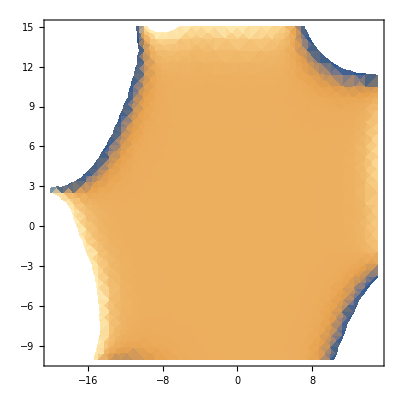

```mathematica
DensityPlot[f[x,y],{x,-20,15},{y,-10,15}]
```

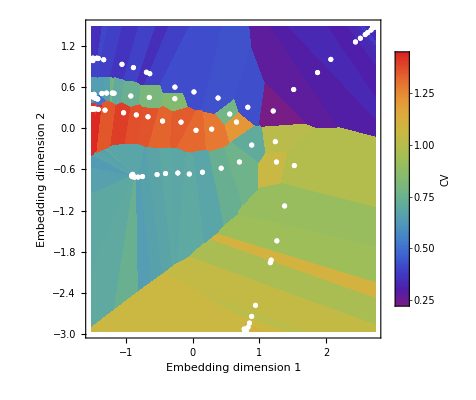

```mathematica
corners = {{-1.6,-2,0.65},{-1.6,1.8,0.6},{3,-2,1.15},{3,1.8,0.38}};
colorkey = ColorData["Rainbow"][#]&/@interpolatedata[[All,2]];
PointData =Table[{interpolatedata[[i,1]]},{i,1,Length[interpolatedata[[All,1]]]}];
InterpolatePlot = Show[{
ListDensityPlot[Join[data],InterpolationOrder->0,Mesh->None,ColorFunction->ColorData["Rainbow"],PlotLegends->BarLegend[Automatic,LegendLabel->"CV"],PlotRange->All,FrameLabel->{"Embedding dimension 1","Embedding dimension 2"}],
ListPlot[PointData,PlotStyle->White]
}]
```

```mathematica
Export[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r500b.pdf"],InterpolatePlot]
```

/home/jdyeakel/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r500b.pdf

```mathematica
ColorData
```

```mathematica
interpolatedata[[All,2]]
```

```mathematica
ColorData[{"Rainbow","Reverse"}][#]&/@interpolatedata[[All,2]]
```

{RGBColor[0.8798122853355085, 0.6325456095186578, 0.22786141579148975],RGBColor[0.8279102931138764, 0.6967829659073866, 0.24909065077783432],RGBColor[0.7791005637861691, 0.7248570574719424, 0.26744564094430684],RGBColor[0.7697826999485297, 0.7270881773972268, 0.27143652769350435],RGBColor[0.7745779817866189, 0.725939969069359, 0.2693826849802215],RGBColor[0.8074420579969512, 0.7117378397214102, 0.25629250865977377],RGBColor[0.781049665171537, 0.7243903540500993, 0.2666108312682644],RGBColor[0.7672225319525872, 0.7277011979271844, 0.27253306019373835],RGBColor[0.7836928317711721, 0.7237574598836843, 0.2654787500592866],RGBColor[0.794246449533546, 0.7212304443269264, 0.26095858384760434],RGBColor[0.7687926858536269, 0.7273252317491616, 0.2718605555824832],RGBColor[0.7160651497732422, 0.7399505993666712, 0.2944440177072476],RGBColor[0.7426355588291407, 0.733588436310789, 0.2830637812850756],RGBColor[0.7086440621852416, 0.7417275448848043, 0.29762250589248485],RGBColor[0.7026814546083272, 0.7426182708539786, 0.30060485396119185],RGBColor[0.746502804330157, 0.7326624420439023, 0.28140742108333544],RGBColor[0.749377164007975, 0.731974189751171, 0.2801763187458776],RGBColor[0.698807791574113, 0.7426630983796192, 0.3029683822673933],RGBColor[0.7340335741233188, 0.7356481422486053, 0.2867480534935394],RGBColor[0.6971327982413303, 0.7426824820497809, 0.3039903849867222],RGBColor[0.6728862938664817, 0.742963071968666, 0.3187844697871358],RGBColor[0.6259317733137514, 0.7435064478264594, 0.34743392572852216],RGBColor[0.6555584055004716, 0.7431635969893412, 0.3293571381576235],RGBColor[0.6513311010638305, 0.7432125169899583, 0.33193644193461275],RGBColor[0.7304553466413497, 0.7365049324712711, 0.28828062586122305],RGBColor[0.6954817918584353, 0.7427015881336887, 0.3049977519892791],RGBColor[0.7292546711131165, 0.7367924287409656, 0.2887948810745645],RGBColor[0.6730085457803223, 0.7429616572222738, 0.31870987737775547],RGBColor[0.7004758608441595, 0.7426437948373873, 0.3019506042878331],RGBColor[0.6821103239972603, 0.742856327927291, 0.31315639730927947],RGBColor[0.7256921555647193, 0.737645456812921, 0.2903207239440939],RGBColor[0.7208254630362019, 0.7388107641043569, 0.29240515220607627],RGBColor[0.7070231024927147, 0.7421156762774815, 0.2983167708732369],RGBColor[0.6991856336313811, 0.7426587258453123, 0.30273784068704973],RGBColor[0.7535034590748783, 0.7309861672492558, 0.27840900634544713],RGBColor[0.7317029314814956, 0.7362062039811543, 0.2877462791596834],RGBColor[0.7200993023856558, 0.738984639954511, 0.29271617037167197],RGBColor[0.7090743731930287, 0.7416245088799568, 0.2974382015788637],RGBColor[0.7166583877792913, 0.7398085512364564, 0.2941899309617537],RGBColor[0.2745906029528139, 0.5077117670845986, 0.7891520673813921],RGBColor[0.2659166259866105, 0.4854953937252816, 0.802655297284797],RGBColor[0.2778506715272397, 0.5158143035261654, 0.7840024910114615],RGBColor[0.29496625017559963, 0.5583531632313675, 0.7569668697191065],RGBColor[0.25779744239446023, 0.4392961266671803, 0.807648289462984],RGBColor[0.27450620599745373, 0.5075020078753208, 0.7892853800885009],RGBColor[0.3235116070482104, 0.6082050752015469, 0.7093650954207489],RGBColor[0.3225793611618427, 0.6070058899723753, 0.7109707638455489],RGBColor[0.27112132660468163, 0.49908926808039955, 0.7946321065570244],RGBColor[0.35770828853158587, 0.6521936365041113, 0.6504659010196433],RGBColor[0.3325388453374953, 0.6198171734419597, 0.6938168889912982],RGBColor[0.3250837926744046, 0.610227440553883, 0.706657216678864],RGBColor[0.3258276759663088, 0.6111843274320378, 0.7053759775433387],RGBColor[0.30545016558280563, 0.5844097644033693, 0.7404065668258434],RGBColor[0.33785265527733177, 0.6266525400374673, 0.6846645645235246],RGBColor[0.3089744696833395, 0.5895053730550301, 0.7344033635376525],RGBColor[0.3505181942716736, 0.6429447302242103, 0.6628498734171616],RGBColor[0.3223787828969094, 0.6067478781150765, 0.7113162329877722],RGBColor[0.31475980214299515, 0.5969472779568551, 0.7244389048113886],RGBColor[0.46546602793943076, 0.10909282971052346, 0.5321128600182189],RGBColor[0.402194290030344, 0.112570660345194, 0.5863491039741264],RGBColor[0.4232469505133423, 0.11141346773458018, 0.5683028598276888],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.4053229226185261, 0.11239869013196163, 0.5836672544484367],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.4708691300290575, 0.1087958397021795, 0.5274813456527887],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.24683353678746348, 0.3049717692843506, 0.7966452231484302],RGBColor[0.24728943119656943, 0.2956552845004308, 0.7934268061195252],RGBColor[0.24971216978578595, 0.3932898177512406, 0.8126204276632644],RGBColor[0.26250372393751736, 0.46607551346027143, 0.8047541035308481],RGBColor[0.2860229448950438, 0.5361255765136487, 0.7710936380647502],RGBColor[0.2691174457396613, 0.49410884593199567, 0.7977974195911168],RGBColor[0.2989667489507858, 0.5682959562648232, 0.750647716152141],RGBColor[0.2935195660337362, 0.5547575913250465, 0.7592520395864323],RGBColor[0.30629586606879966, 0.5860597779214574, 0.7390168987747773],RGBColor[0.36918641335560554, 0.6615442800028813, 0.632465687585515],RGBColor[0.3423562016550593, 0.6324456321540786, 0.6769078102979685],RGBColor[0.36335218701527006, 0.6576675248339695, 0.6413287287854155],RGBColor[0.38076961472242987, 0.6692411421319568, 0.6148691143721756],RGBColor[0.3894640177326736, 0.6750184414419844, 0.6016610474249655],RGBColor[0.3580450495062834, 0.6526268256364252, 0.6498858754366036],RGBColor[0.5172110632951865, 0.7304755371240421, 0.4373767191867581],RGBColor[0.4647940295013199, 0.7135886161547299, 0.498650820311313],RGBColor[0.41147735841057786, 0.6896459734024902, 0.5682195705273637],RGBColor[0.465322755131306, 0.7137662034375218, 0.4980204680164141],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016]}

```mathematica
keyList={1,2,3};
keys=RandomChoice[keyList,10];(*Dummy keys*)pts=RandomInteger[100,{Length@keys,2}];(*Dummy Points*)colors[key_]:=Hue[key/Length@keyList]
```

```mathematica
colors/@keys
```

{Hue[Rational[1, 3]],Hue[1],Hue[1],Hue[1],Hue[1],Hue[Rational[2, 3]],Hue[Rational[1, 3]],Hue[1],Hue[Rational[2, 3]],Hue[Rational[1, 3]]}

```mathematica
Transpose@{pts}
```

{{{43,40}},{{62,49}},{{5,63}},{{44,17}},{{30,82}},{{1,80}},{{64,3}},{{65,22}},{{0,57}},{{19,71}}}

```mathematica
Length[interpolatedata[[All,1]]]
```

115

```mathematica
PD =Table[{interpolatedata[[i,1]]},{i,1,Length[interpolatedata[[All,1]]]}]
```

{{{1.0423,0.080038}},{{1.7456,-0.280722}},{{2.03857,-0.341186}},{{2.35592,-0.355224}},{{2.67323,-0.476496}},{{2.75202,-0.496239}},{{2.84107,-0.524785}},{{2.88049,-0.535731}},{{2.90083,-0.542695}},{{2.96441,-0.559177}},{{2.97837,-0.56182}},{{2.982,-0.567846}},{{2.97804,-0.569268}},{{2.97037,-0.56763}},{{2.95305,-0.56303}},{{2.95149,-0.562654}},{{2.94925,-0.562111}},{{2.94649,-0.561437}},{{2.94292,-0.560561}},{{2.93868,-0.559499}},{{0.816276,-0.446966}},{{0.736219,-0.898459}},{{0.521823,-0.973004}},{{0.252161,-1.0638}},{{-0.079507,-1.243}},{{-0.13294,-1.26788}},{{-0.29337,-1.33092}},{{-0.438553,-1.38098}},{{-0.680242,-1.46452}},{{-0.750551,-1.48452}},{{-0.76929,-1.48557}},{{-0.822476,-1.47025}},{{-0.842059,-1.45474}},{{-0.854069,-1.4366}},{{-0.855097,-1.43151}},{{-0.854848,-1.42405}},{{-0.853174,-1.41636}},{{-0.849423,-1.40474}},{{-0.844259,-1.39201}},{{0.465801,-0.187684}},{{0.00962795,-0.332212}},{{-0.357388,-0.30838}},{{-0.700965,-0.280418}},{{-0.908087,-0.325572}},{{-1.09941,-0.373127}},{{-1.2465,-0.401388}},{{-1.37927,-0.412958}},{{-1.56677,-0.42756}},{{-1.60314,-0.426457}},{{-1.61879,-0.41986}},{{-1.61993,-0.412036}},{{-1.60976,-0.402247}},{{-1.59165,-0.393979}},{{-1.58682,-0.391942}},{{-1.57968,-0.389368}},{{-1.57217,-0.386897}},{{-1.56207,-0.383738}},{{-1.5502,-0.380048}},{{1.02675,0.447344}},{{1.10349,0.798867}},{{0.715661,1.47651}},{{0.65183,1.83738}},{{0.50081,2.06021}},{{0.282962,2.40399}},{{0.0354643,2.82437}},{{-0.00162233,2.88268}},{{-0.145599,3.07647}},{{-0.188072,3.13635}},{{-0.21785,3.17137}},{{-0.239766,3.18832}},{{-0.241553,3.18829}},{{-0.251951,3.17661}},{{-0.259905,3.15319}},{{-0.260676,3.14856}},{{-0.260746,3.14775}},{{-0.261178,3.12973}},{{-0.260938,3.11791}},{{0.966297,0.335948}},{{0.732655,0.240501}},{{0.698918,0.180732}},{{0.459333,0.0863302}},{{0.306097,-0.034219}},{{0.139565,-0.142939}},{{-0.019008,-0.244354}},{{-0.155881,-0.325228}},{{-0.379783,-0.453523}},{{-0.442881,-0.490277}},{{-0.485702,-0.516305}},{{-0.5108,-0.532206}},{{-0.528399,-0.541159}},{{-0.53951,-0.548701}},{{-0.540444,-0.549709}},{{-0.540496,-0.549964}},{{-0.539668,-0.549455}},{{-0.538122,-0.548411}},{{-0.535063,-0.54609}},{{0.658081,0.316417}},{{-0.0329012,0.237909}},{{-0.355887,0.0878692}},{{-0.643523,0.051178}},{{-0.845694,0.0123355}},{{-1.02186,-0.0338871}},{{-1.17655,-0.09953}},{{-1.31305,-0.152825}},{{-1.55165,-0.22342}},{{-1.59718,-0.235571}},{{-1.64368,-0.252226}},{{-1.66387,-0.262385}},{{-1.6723,-0.271103}},{{-1.66825,-0.273806}},{{-1.66589,-0.273921}},{{-1.66144,-0.273763}},{{-1.65361,-0.273221}},{{-1.64664,-0.272468}},{{-1.63288,-0.27062}}}

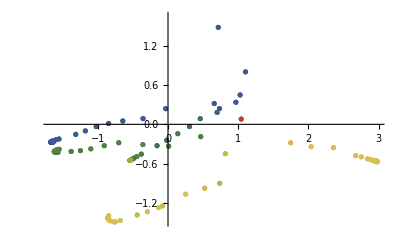

```mathematica
ListPlot[PD,PlotStyle->{RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.8696881658265921, 0.7043270676283682, 0.32394716443532673],RGBColor[0.8739954580975888, 0.7331538524942828, 0.32549368817882374],RGBColor[0.8658814761867227, 0.7375644740113905, 0.322560781913951],RGBColor[0.8410270503492879, 0.7510749139653102, 0.3135768203955247],RGBColor[0.859131678299899, 0.741233548471106, 0.32012097803881795],RGBColor[0.8525144837120885, 0.7448305420499062, 0.31772910538299143],RGBColor[0.8452698270693142, 0.7487686132489417, 0.31511042825407276],RGBColor[0.8458407381040248, 0.7484582757941988, 0.31531679161164267],RGBColor[0.8456714506618799, 0.7485502975466629, 0.3152556004227683],RGBColor[0.841485047966301, 0.7508259543094258, 0.3137423697022634],RGBColor[0.8510761859640394, 0.7456123760575785, 0.3172092136057672],RGBColor[0.8460707279765938, 0.748333257240816, 0.31539992449824816],RGBColor[0.8360366624012392, 0.7537876033333877, 0.3117729785534105],RGBColor[0.8413946177545323, 0.7508751106228371, 0.3137096825040981],RGBColor[0.8417231760570006, 0.7506965119601322, 0.3138284442556365],RGBColor[0.8194026306021135, 0.7628295779613107, 0.3057603873731892],RGBColor[0.8441518385798461, 0.7493763326328022, 0.3147063165021812],RGBColor[0.8195229115026591, 0.7627641953250328, 0.30580386449830854],RGBColor[0.816427250348703, 0.7644469436778518, 0.30468489675939825],RGBColor[0.7557442170357574, 0.7379805323789776, 0.2915348502529898],RGBColor[0.7069677175380747, 0.713875738827029, 0.28138330788196697],RGBColor[0.7727640614891491, 0.7463915467211358, 0.295077082145318],RGBColor[0.8301732379750539, 0.7569748603697183, 0.3096535661093013],RGBColor[0.7670285889260829, 0.7435571411471535, 0.2938833947478743],RGBColor[0.80392993864197, 0.7617933701888046, 0.30156343778184713],RGBColor[0.829298284336569, 0.7574504701734824, 0.3093373025242976],RGBColor[0.7430565067248007, 0.7317104096591815, 0.2888942378650701],RGBColor[0.8379027202319733, 0.7527732462753097, 0.3124474898799697],RGBColor[0.8263319389900837, 0.7590629246694506, 0.30826507769731937],RGBColor[0.8169855768612, 0.7641434469537226, 0.3048867112746801],RGBColor[0.8239916369857643, 0.7603350727331477, 0.30741914453089575],RGBColor[0.8242960442771878, 0.76016960214617, 0.3075291765795122],RGBColor[0.854219754681691, 0.7439035859741284, 0.31834549816830876],RGBColor[0.81645217530312, 0.7644333948997706, 0.3046939062144062],RGBColor[0.8312668590682717, 0.7563803866848744, 0.31004886994297143],RGBColor[0.8511358711197627, 0.7455799322297542, 0.3172307875960797],RGBColor[0.8222617650135629, 0.7612754014923498, 0.3067938593872473],RGBColor[0.8295902056960082, 0.7572917867251596, 0.30944282136737056],RGBColor[0.30661084498470303, 0.48664539509048754, 0.2678243493300593],RGBColor[0.2938526791309044, 0.47866164791721794, 0.27084637763327923],RGBColor[0.3481925489325801, 0.5126662052255709, 0.25797488603991214],RGBColor[0.2987956807866752, 0.48175485707823357, 0.26967552822766855],RGBColor[0.3121516784981232, 0.4901127127603825, 0.2665118914193479],RGBColor[0.34650542592149397, 0.5116104450383253, 0.2583745150735007],RGBColor[0.30560172538098473, 0.4860139128009484, 0.2680633796137785],RGBColor[0.30824931355618546, 0.4876707085231523, 0.267436245079519],RGBColor[0.32707203527114725, 0.4994495059621528, 0.26297770468914533],RGBColor[0.28001842914215896, 0.45424430078136885, 0.3194628353825441],RGBColor[0.28642615533440047, 0.46707349551606453, 0.2925730839466877],RGBColor[0.30503685826592114, 0.4856604328191986, 0.26819717975627877],RGBColor[0.39382643088575525, 0.5412227689373137, 0.24716558285098753],RGBColor[0.30917640551131165, 0.48825085992272793, 0.26721664469493517],RGBColor[0.3056595267395215, 0.4860500834729805, 0.26804968819892594],RGBColor[0.34785490688986775, 0.5124549171191948, 0.25805486335178646],RGBColor[0.3800947752671187, 0.5326298357535082, 0.2504182017936417],RGBColor[0.37892811746262506, 0.5318997699230795, 0.2506945481702098],RGBColor[0.331867770458447, 0.502450559380341, 0.2618417383098987],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24503571670657479, 0.34236065345607014, 0.56733305687861],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24011240084299393, 0.3409135110363509, 0.5725802628904264],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24054097551939707, 0.3410394847929462, 0.5721234935746143],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.23959381740754793, 0.3407610804167458, 0.5731329623709187],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.23844886195530168, 0.3404245361751116, 0.574353240999948],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24263127220299613, 0.3416538993632181, 0.5698956825568822],RGBColor[0.2382655527614883, 0.3403706549053247, 0.5745486095544854],RGBColor[0.2515639934192704, 0.3442795525111748, 0.560375304468887],RGBColor[0.2583237561534516, 0.37877893939347723, 0.4830108778223839],RGBColor[0.26428140793431626, 0.42198269763468177, 0.3872090281206404],RGBColor[0.2612284646365972, 0.3998433331652103, 0.4363017958274455],RGBColor[0.288514173934268, 0.47125401079148327, 0.2838108023729427],RGBColor[0.28237616264662835, 0.4589648243109133, 0.30956870664091096],RGBColor[0.2674835023382857, 0.4291475641032694, 0.37206512454260815],RGBColor[0.2845991267053834, 0.46341551991531166, 0.3002401321673105],RGBColor[0.35632432011710147, 0.5177548681221085, 0.25604871240676286],RGBColor[0.2755251315618696, 0.44524806905594555, 0.3383187682729989],RGBColor[0.33527622653458955, 0.5045834875672727, 0.2610343769030615],RGBColor[0.38593065850716096, 0.5362817883033605, 0.2490358554181677],RGBColor[0.4624754826129366, 0.5814186858886284, 0.24678818471165606],RGBColor[0.3971973212044433, 0.5433321893948958, 0.24636711964970437],RGBColor[0.5095833683745711, 0.6080731281196481, 0.25186702906667013],RGBColor[0.5127541000212, 0.6098671819630487, 0.25220887528337854],RGBColor[0.5492872590378963, 0.6305382641138049, 0.2561476262046498],RGBColor[0.6422489236833656, 0.6818924439849503, 0.2679137972614112],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.789084045455776, 0.43880561979057575, 0.2827219735998753],RGBColor[0.8274152932273967, 0.5663685201194278, 0.3087207964033088],RGBColor[0.8514567052354841, 0.6448282527273054, 0.31738033063263116],RGBColor[0.8684509855256598, 0.7002894996366784, 0.3235015414760695],RGBColor[0.8754026067392908, 0.7323889506070173, 0.3260023206988603],RGBColor[0.861601051295327, 0.7398912396285371, 0.32101356562505595],RGBColor[0.8558804228693497, 0.7430008752062556, 0.31894576868714447],RGBColor[0.8476922851644353, 0.7474518065421971, 0.31598605782801326],RGBColor[0.8389752451988832, 0.7521902400832016, 0.31283516823928054],RGBColor[0.8357770251399115, 0.753928737699231, 0.31167912922533614],RGBColor[0.8263015614440904, 0.7590794373828713, 0.3082540973308441],RGBColor[0.8245745215956776, 0.7600182266481162, 0.3076298358958621],RGBColor[0.8212956675527991, 0.7618005555159694, 0.3064446506601047],RGBColor[0.8176971849735197, 0.7637566289787229, 0.30514393145506546],RGBColor[0.804257921909342, 0.7619554558044168, 0.3016316988516246],RGBColor[0.7945939909678207, 0.7571796505981263, 0.2996204064170752],RGBColor[0.7880564245942926, 0.7539488593484684, 0.2982597843403024],RGBColor[0.7789364664584125, 0.7494418793410522, 0.296361705503326],RGBColor[0.7742856136884456, 0.7471434805831445, 0.29539375311965915]}]
```

```mathematica
ListPlot[PointData,ColorFunction->ColorData[{"DarkRainbow","Reverse"}][#]&/@interpolatedata[[All,2]]]
```

-Graphics-